0.0001

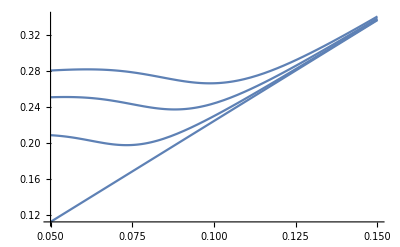

```mathematica
Ω := √(Subscript[ω, R]^2+(3 L (1+L))/((-Subscript[ω, R]^2/(12 Subscript[λ, R])+(1/2 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))-√(Subscript[ω, R]^12/(4096 Subscript[λ, R]^6)+1/4 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))^2))^(1/3)+(1/2 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))+√(Subscript[ω, R]^12/(4096 Subscript[λ, R]^6)+1/4 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))^2))^(1/3))^2)+12 Subscript[λ, R] (-Subscript[ω, R]^2/(12 Subscript[λ, R])+(1/2 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))-√(Subscript[ω, R]^12/(4096 Subscript[λ, R]^6)+1/4 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))^2))^(1/3)+(1/2 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))+√(Subscript[ω, R]^12/(4096 Subscript[λ, R]^6)+1/4 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))^2))^(1/3)))
Subscript[λ, R] = 0.0001
L = {0,1,2,3};
Plot[Re[Ω],{Subscript[ω, R], 0.05, 0.15}]
```

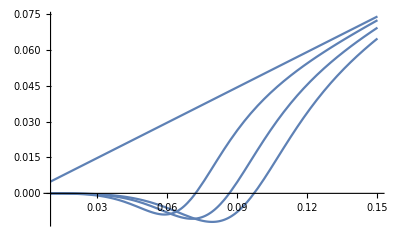

```mathematica
Plot[Im[Ω],{Subscript[ω, R], 0.01, 0.15}]
```